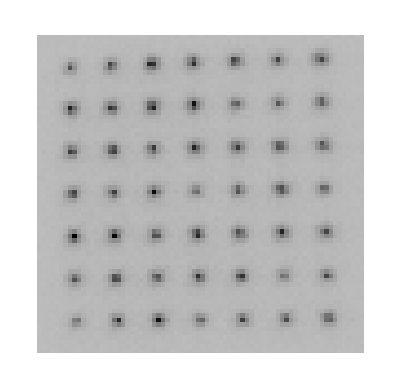

```mathematica
SetDirectory["C:/Users/zhouyu/Desktop/S41"];
filenames=FileNames["*.tga"];


matrixlist=Table[Partition[Import[filenames[[i]],"UnsignedInteger16"][[10;;]],140],{i,1,300}];


avgmatrix=Mean[matrixlist];


croppedmatrixlist=matrixlist[[All,220-99;;220-28,34;;107]];
croppedavgmatrix=avgmatrix[[220-99;;220-28,34;;107]];

ArrayPlot[croppedavgmatrix]
```

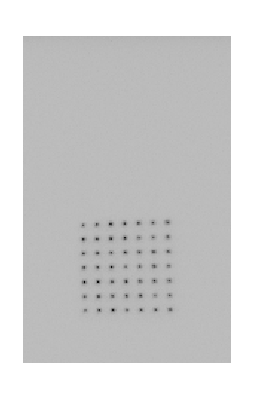

```mathematica
ArrayPlot[avgmatrix]
```

10452037/25392

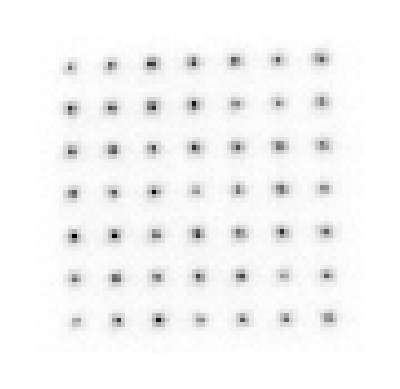

```mathematica
bgnoise=Mean[Flatten[avgmatrix[[220-155;;220-110,32;;77]]]]   (*(32,155)to(77,110)*)
subtrcroppedavgmatrix=croppedavgmatrix-bgnoise;
ArrayPlot[subtrcroppedavgmatrix]
```

```mathematica
(*MatrixForm[subtravgmatrix]；*)
Dimensions[subtrcroppedavgmatrix]
```

{72,74}

{72,74}

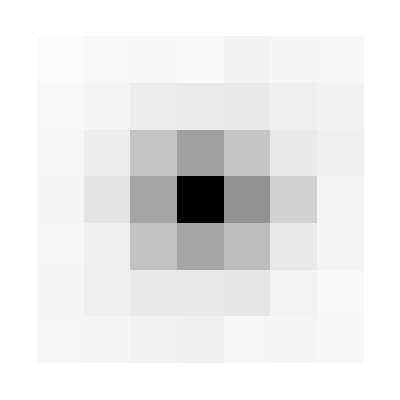

```mathematica
{72,74}
(*selected atom coordinate (28,7)->region(25-31,4-10)*)

ArrayPlot[subtrcroppedavgmatrix[[72-10;;72-4,25;;31]]]
```

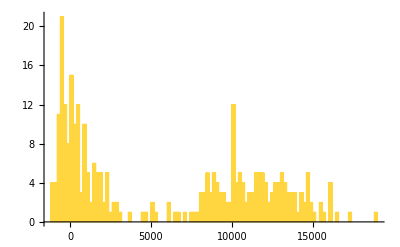

```mathematica
subtrcroppedmatrixlist=croppedmatrixlist-bgnoise;
countlist=Table[Total[Flatten[subtrcroppedmatrixlist[[i,72-10;;72-4,25;;31]]]],{i,1,300}];
Histogram[countlist,60]
```

```mathematica
(*calculating loading rate*)
loadingrate=N[Length[Cases[countlist,_?(#>5000&)]]/Length[countlist]]
```

0.503333

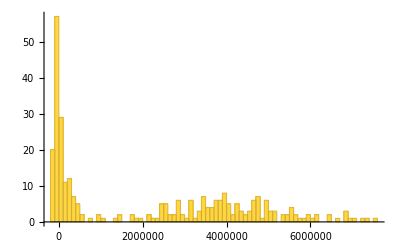

0.5

```mathematica
(*shape function and inner product(weighting)*)
ipcountlist=Table[Total[Flatten[subtrcroppedmatrixlist[[i,72-10;;72-4,25;;31]]*subtrcroppedavgmatrix[[72-10;;72-4,25;;31]]]],{i,1,300}];
Histogram[ipcountlist,60]
loadingratemethod2=N[Length[Cases[ipcountlist,_?(#>1500000&)]]/Length[ipcountlist]]
(*set up threshold as 5000000*)
```

```mathematica
ImageAdjust[Image[subtrcroppedavgmatrix]]
```

-Graphics-

```mathematica
N[subtrcroppedavgmatrix[[65,56]]]
```

316.13

```mathematica
ClearAll[maxdetectedmatrix]
maxdetectedmatrix=MaxDetect[subtrcroppedavgmatrix,20];
ArrayPlot[maxdetectedmatrix]
```

-Graphics-

```mathematica
(*extract the center of the atom*)
centerlist=Position[maxdetectedmatrix,1];
centerlist=DeleteCases[centerlist,{15,65}]
Dimensions[centerlist]
```

{{6,45},{6,55},{6,65},{7,17},{7,26},{7,36},{8,8},{16,36},{16,46},{16,55},{16,65},{17,8},{17,17},{17,27},{25,65},{26,27},{26,36},{26,46},{26,55},{27,8},{27,18},{35,56},{35,65},{36,9},{36,18},{36,27},{36,37},{36,46},{45,46},{45,56},{45,66},{46,9},{46,18},{46,27},{46,37},{55,28},{55,37},{55,47},{55,56},{55,66},{56,9},{56,18},{65,10},{65,19},{65,28},{65,38},{65,47},{65,57},{65,67}}

{49,2}

```mathematica
(*set up ROI*)
roilist=Table[{i[[1]]-3,i[[1]]+3,i[[2]]-3,i[[2]]+3},{i,centerlist}]
```

{{3,9,42,48},{3,9,52,58},{3,9,62,68},{4,10,14,20},{4,10,23,29},{4,10,33,39},{5,11,5,11},{13,19,33,39},{13,19,43,49},{13,19,52,58},{13,19,62,68},{14,20,5,11},{14,20,14,20},{14,20,24,30},{22,28,62,68},{23,29,24,30},{23,29,33,39},{23,29,43,49},{23,29,52,58},{24,30,5,11},{24,30,15,21},{32,38,53,59},{32,38,62,68},{33,39,6,12},{33,39,15,21},{33,39,24,30},{33,39,34,40},{33,39,43,49},{42,48,43,49},{42,48,53,59},{42,48,63,69},{43,49,6,12},{43,49,15,21},{43,49,24,30},{43,49,34,40},{52,58,25,31},{52,58,34,40},{52,58,44,50},{52,58,53,59},{52,58,63,69},{53,59,6,12},{53,59,15,21},{62,68,7,13},{62,68,16,22},{62,68,25,31},{62,68,35,41},{62,68,44,50},{62,68,54,60},{62,68,64,70}}

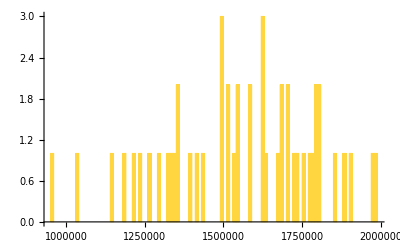

```mathematica
(*process all atoms in one go*)
lightstrengthlist=Table[Total[Flatten[Table[subtrcroppedmatrixlist[[i,j[[1]];;j[[2]],j[[3]];;j[[4]]]],{i,1,300}]]],{j,roilist}];

Histogram[lightstrengthlist,120]
(*we can see that atoms in different position have different light strength, thus before get the histogram we need to do renormalization*)
```

```mathematica
Dimensions[subtrcroppedmatrixlist]
```

{300,72,74}

```mathematica
weightlist=Mean[lightstrengthlist]/lightstrengthlist;
signaloverroi[roi_,w_]:=Module[{rawsignal,weightedsignal},
rawsignal=Table[Total[Flatten[subtrcroppedmatrixlist[[i,roi[[1]];;roi[[2]],roi[[3]];;roi[[4]]]]]],{i,1,300}];
weightedsignal=rawsignal w;
weightedsignal]

allatomscountlist=Flatten[MapThread[signaloverroi,{roilist,weightlist}]];
```

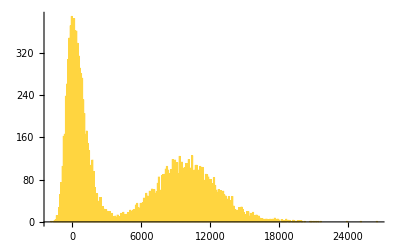

```mathematica
f11=Histogram[allatomscountlist,300]
```

```mathematica
loadingrate=N[Length[Cases[allatomscountlist,_?(#>3611&)]]/Length[allatomscountlist]]
```

0.490204

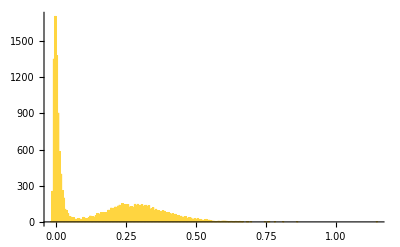

```mathematica
signaloverroi2[roi_,w_]:=Module[{rawsignal,weightedsignal},
rawsignal=Table[Total[Flatten[subtrcroppedmatrixlist[[i,roi[[1]];;roi[[2]],roi[[3]];;roi[[4]]]]*subtrcroppedavgmatrix[[roi[[1]];;roi[[2]],roi[[3]];;roi[[4]]]]]],{i,1,300}];
weightedsignal=rawsignal w;
weightedsignal]

allatomscountlist2=Flatten[MapThread[signaloverroi2,{roilist,weightlist}]];
f21=Histogram[allatomscountlist2,300]
```

```mathematica
loadingrate=N[Length[Cases[allatomscountlist2,_?(#>720000&)]]/Length[allatomscountlist2]]
```

0.492245

FittedModel[…]

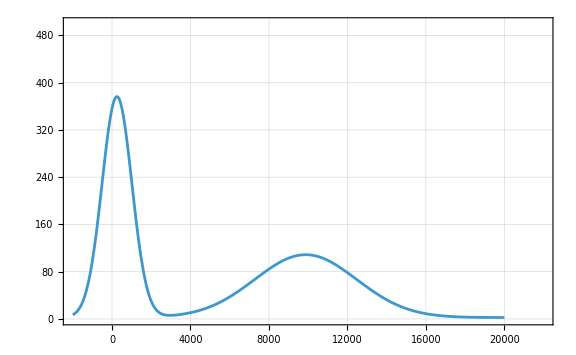

```mathematica
(*do double gaussian fitting and calculate fidelities*)
twogaussmodel=baseline+amp1 Exp[-(x-center1)^2/(2 σ1^2)]+amp2 Exp[-(x-center2)^2/(2 σ2^2)];
fitdata=Transpose[{MovingAverage[HistogramList[allatomscountlist,300][[1]],2],HistogramList[allatomscountlist,300][[2]]}];
nlm=NonlinearModelFit[fitdata,twogaussmodel,{{baseline,0},{amp1,300},{center1,0},{σ1,3000},{amp2,100},{center2,10000},{σ2,5000}},{x}]
f12=Plot[nlm[x],{x,-2000,20000},Frame->True,Axes->False,FrameLabel->{"",""},LabelStyle->Directive[Black,13,FontFamily->"Helvetica"],PlotRange->{{-2000,22000},{0,500}},ImageSize->Large,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed]]
```

FittedModel[…]

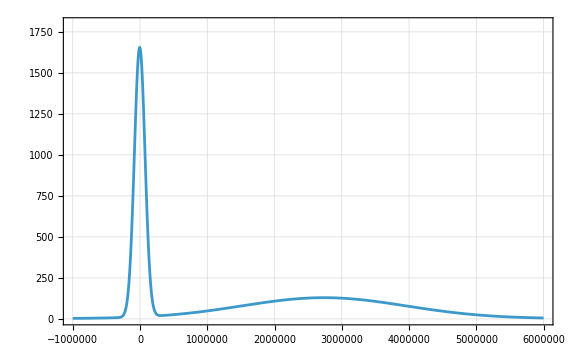

```mathematica
(*innerproduct method*)
twogaussmodel2=baseline2+amp12 Exp[-(x-center12)^2/(2 σ12^2)]+amp22 Exp[-(x-center22)^2/(2 σ22^2)];
fitdata2=Transpose[{MovingAverage[HistogramList[allatomscountlist2,300][[1]],2],HistogramList[allatomscountlist2,300][[2]]}];
nlm2=NonlinearModelFit[fitdata2,twogaussmodel2,{{baseline2,0},{amp12,1500},{center12,100000},{σ12,200000},{amp22,150},{center22,4000000},{σ22,2000000}},{x}]
f22=Plot[nlm2[x],{x,-1000000,6000000},Frame->True,Axes->False,FrameLabel->{"",""},LabelStyle->Directive[Black,13,FontFamily->"Helvetica"],PlotRange->{{-1000000,6000000},{0,1800}},ImageSize->Large,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed]]
```

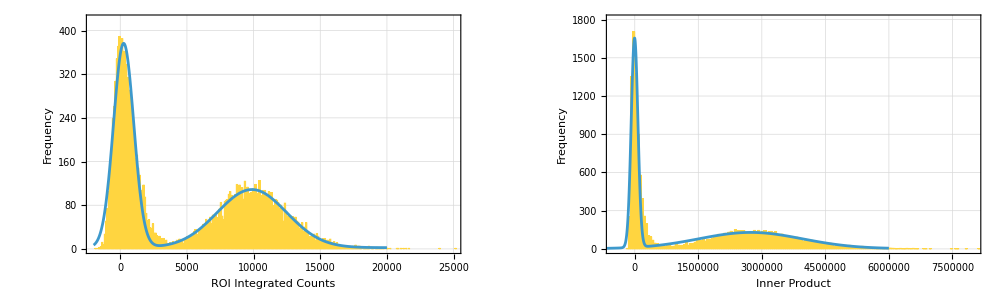

```mathematica
(*put 4 figures together*)
(*fig1=Show[f11,f12];
fig2=Show[f21,f22];
GraphicsRow[{fig1,fig2}]*)
fig1=Show[f11,f12,Frame->True,Axes->False,FrameLabel->{"ROI Integrated Counts","Frequency"},LabelStyle->Directive[Black,13,FontFamily->"Helvetica"],PlotRange->{{-2000,25000},{0,420}},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed]];


fig2=Show[f21,f22,Frame->True,Axes->False,FrameLabel->{"Inner Product","Frequency"},LabelStyle->Directive[Black,13,FontFamily->"Helvetica"],PlotRange->{{-500000,8*^6},{0,1800}},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Dashed]];


GraphicsRow[{fig1,fig2},ImageSize->1000,Spacings->30]

(*note some plotting pararmaeter is ai generated, and it is just to make the figures prittier*)
```

```mathematica
(*use some posibility knowledge to get fidelities*)
threshold1=Range[1700,5000];
Off[NIntegrate::ncvb]
params1=nlm["BestFitParameters"];
total=NIntegrate[(nlm[x]-baseline)/.params1,{x,-Infinity,Infinity}];
fidelities=Table[1-(NIntegrate[amp1 Exp[-(x-center1)^2/(2 σ1^2)]/.params1,{x,t1,Infinity}]+NIntegrate[amp2 Exp[-(x-center2)^2/(2 σ2^2)]/.params1,{x,-Infinity,t1}])/total,{t1,threshold1}];
```

```mathematica
bestthreshold1=threshold1[[Position[fidelities,Max[fidelities]][[1,1]]]]
bestfidelities1=Max[fidelities]
```

2680

0.998255

```mathematica
threshold2=Range[235700,236000];
Off[NIntegrate::ncvb]
params2=nlm2["BestFitParameters"];

total2=NIntegrate[(nlm2[x]-baseline2)/. params2,{x,-Infinity,Infinity}];
fidelities2=Table[1-(NIntegrate[amp12 Exp[-(x-center12)^2/(2 σ12^2)]/. params2,{x,t2,Infinity}]+NIntegrate[amp22 Exp[-(x-center22)^2/(2 σ22^2)]/. params2,{x,-Infinity,t2}])/total2,{t2,threshold2}];
bestthreshold2=threshold2[[Position[fidelities2,Max[fidelities2]][[1,1]]]]
bestfidelities2=Max[fidelities2]
```

235771

0.988292